```mathematica
(* notebook to manipulate the stringbit numerical results. *)
(* depends on perturb.nb *)

ClearAll[ResultFolder,LoadEnergyData,LoadTotalEnergy,LoadEvsS];
ResultFolder = NotebookDirectory[]<>"../results/";
Format[energy,StandardForm]="E";

Options[LoadTotalEnergy]={Folder->ResultFolder,NormalizeFactorM->0};
LoadTotalEnergy[s_,xi_,opts:OptionsPattern[]]:=Module[{file,data,normpower},
file = "Es="<> ToString[s] <> "xi="<>ToString[xi];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];

normpower = OptionValue[NormalizeFactorM];
data=data[[2;;Length[data]]];
Do[data[[i,2]]=N[data[[i,2]]/data[[i,1]]^normpower], {i,1,Length[data]}];
Return[data];
];

(*DataSet: 0 for all data point, 1 for odd only, 2 for even only *)
Options[LoadEvsS]={LogData->False,DataSet->0,Folder->ResultFolder};
LoadEvsS[M_,xi_,opts:OptionsPattern[]]:=Module[{file,data,i,len,ret={}},
file = "Exi="<> ToString[xi] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
data=data[[2;;Length[data]]];
If[OptionValue[LogData],
For[i=1,i≤ Length[data],i++,
data[[i,2]]=Log10[Abs[data[[i,2]]]];
];
];

If[OptionValue[DataSet]==0, Return[data]];

len = Length[data];
For[i=1,i≤Length[data],i++,
If[Mod[data[[i,1]],2]== Mod[OptionValue[DataSet],2],
AppendTo[ret, data[[i]]];
];
];
Return[ret];

(*If[OptionValue[DataSet] == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];*)
];


(*DataSet: 0 for all data point, 1 for odd only, 2 for even only, 3 for data[L] + data[M-L] *)
Options[LoadEnergyData]={DataSet->0,NormalizeFactorM->0,Folder->ResultFolder};
LoadEnergyData[s_,xi_,M_,opts:OptionsPattern[]]:=Module[{file,data,dataType, ret, len,normpower},
file = "s="<>ToString[s]<>"-M="<>ToString[M];
If[xi≠0, file = file <> "-xi="<>ToString[xi]];
data=Import[OptionValue[Folder]<>file<>".txt","Table"];

normpower = OptionValue[NormalizeFactorM];
data=data[[2;;Length[data],{2,3}]];
Do[data[[i,1]]=N[data[[i,1]]/M];data[[i,2]]=N[data[[i,2]]/(M^normpower)], {i,1,Length[data]}];

dataType = OptionValue[DataSet];
If[dataType == 0,  Return[data]];
len = Length[data];

If[dataType == 3,
Return[Table[{data[[2i-1,1]], data[[2i-1,2]]+data[[len-2i+2,2]]},{i,1,Round[len/2]}]]
];

If[dataType == 1, 
Return[Table[data[[2*i-1]],{i,1,Floor[(len+1)/2]}]]
];

If[dataType == 2,
Return[Table[data[[2*i]],{i,1,Floor[len/2]}]]
];
];

AxesFontSize=14;
LabelFontSize = 16;

ClearAll[PlotEnergyCorrection];
Options[PlotEnergyCorrection]=Join[{LegendPos->{0.15,70}},Options[ListPlot],Options[LoadEnergyData]];
PlotEnergyCorrection[s_,xi_,Mlist_,showLegends_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,toPlot,m,options},
For[i=1,i≤ Length[Mlist],i++,
m = Mlist[[i]];
toPlot=LoadEnergyData[s,xi,m, FilterRules[{opts},Options[LoadEnergyData]]];
AppendTo[data,toPlot];
AppendTo[labels, Style["M="<>ToString[m],FontSize->LabelFontSize]];
];

If[showLegends,
options=Join[{PlotLegends->Placed[labels,OptionValue[LegendPos]],AxesLabel->{Style["i=L/M",FontSize->AxesFontSize], Style["Δ(Ê)_i",FontSize->AxesFontSize]}},FilterRules[{opts},Options[ListPlot]]],
options = Join[{AxesLabel->{Style["i=L/M",FontSize->AxesFontSize], Style["Δ(Ê)_i",FontSize->AxesFontSize]}},FilterRules[{opts},Options[ListPlot]]]
];

Return[ListPlot[data,options]]
];

ClearAll[PlotTotalEnergy]
Options[PlotTotalEnergy]=Join[{LegendPos->{0.15,70}},Options[ListPlot],Options[LoadTotalEnergy]];
PlotTotalEnergy[sList_,xi_,opts:OptionsPattern[]]:=Module[{data={},labels={},i,j,s,pos},
For[j=1,j≤ Length[sList],j++,
s=sList[[j]];
For[i=1,i≤Length[xi],i++,
AppendTo[data,LoadTotalEnergy[s,xi[[i]],FilterRules[{opts},Options[LoadEnergyData]]]];
AppendTo[labels, Style["ξ="<>ToString[xi[[i]]],FontSize->LabelFontSize]];
];
];

pos = OptionValue[LegendPos];
Return[ListPlot[data,Join[{PlotLegends->Placed[labels,pos],AxesLabel->{Style["M",FontSize->AxesFontSize], Style["ΔE",FontSize->AxesFontSize]}},FilterRules[{opts},Options[ListPlot]]]]]
];

ClearAll[PlotEvsS];
Options[PlotEvsS]=Join[{LegendPos->{0.15,70}, YLabel->"ln|ΔE|"},Options[ListPlot],Options[LoadEvsS]];
PlotEvsS[MList_, xi_, opts:OptionsPattern[]]:=Module[{i,data={},labels={},tmp,j},
For[i=1,i≤Length[MList],i++,
(*AppendTo[data,LoadEvsS[MList[[i]],xi,LogData->True, DataSet->1]];
AppendTo[data,LoadEvsS[MList[[i]],xi,LogData->True, DataSet->2]];*)
tmp = LoadEvsS[MList[[i]],xi,FilterRules[{opts},Options[LoadEvsS]]];
For[j=1,j≤ Length[tmp],j++,
tmp[[j,2]]/=3/2Pi*2^tmp[[j,1]]/tmp[[j,1]]*MList[[i]]^(5-tmp[[j,1]]/4)
];

AppendTo[data,tmp];
(*AppendTo[labels, "M="<>ToString[MList[[i]]]<>" odd s"];
AppendTo[labels, "M="<>ToString[MList[[i]]] <> " even s"];*)
AppendTo[labels, Style["M="<>ToString[MList[[i]]],FontSize->LabelFontSize]];
];

Return[ListPlot[data,Join[{PlotLegends->Placed[labels,OptionValue[LegendPos]],AxesLabel->{Style["s",FontSize->AxesFontSize], Style[OptionValue[YLabel],FontSize->AxesFontSize]},PlotMarkers->Automatic},FilterRules[{opts},Options[ListPlot]]]]]
];

DltEArray={{3,-0.294229},{5,1.51612},{7,8.84788},{9,24.8366},{11,52.4987},{13,94.7675},{15,154.512},{17,234.55},{19,337.654},{21,466.562},{23,623.977},{25,812.573},{27,1035},{29,1293.88}};
DeltaE[M_,x_]:=-4Cot[Pi/(2*M)]+DltEArray[[(M-1)/2,2]]*x^2;

ClearAll[PlotLowestEnergy];
PlotLowestEnergy[M_,minN_,maxN_,color_]:=Module[{file,mat1,mat2,mat3,mat4,cmat,vmat, plot},
file = ToString[M]<>"h0Ham-";
mat1=LoadSparseMatFromFile[file <> "re-0.dat"];
mat2=LoadSparseMatFromFile[file <> "re-1.dat"];
mat3=LoadSparseMatFromFile[file <> "im-0.dat"];
mat4=LoadSparseMatFromFile[file <> "im-1.dat"];
cmat=N[mat1 + I*mat3];
vmat = N[mat2 + I * mat4];

plot=Plot[{-Re[First[Eigenvalues[-cmat - vmat *x,1,Method->{Arnoldi,MaxIterations->10^5,Criteria->RealPart}]]],DeltaE[M,x]},
{x,N[1/maxN],N[1/minN]+.2},PlotStyle->{color,Directive[color,Dashed]},AxesOrigin->Automatic,AxesLabel->{Style["1/N",FontSize->AxesFontSize],Style["E",FontSize->AxesFontSize]}, PlotLegends->Placed[LineLegend[{color},{Style["M="<>ToString[M],FontSize->LabelFontSize]}],{0.15,0.70}]
];

Return[plot];
];
```

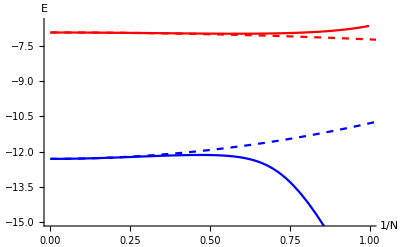

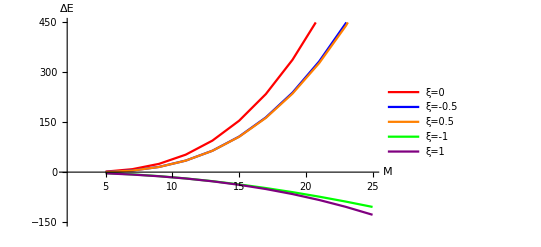

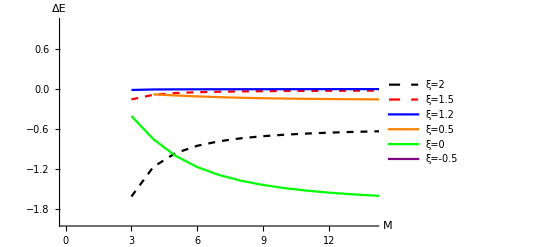

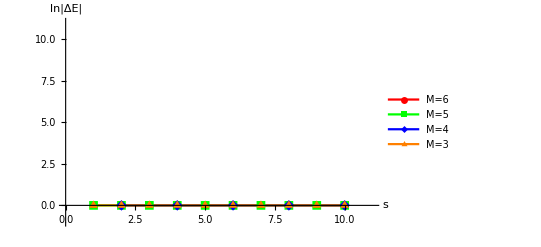

```mathematica
(* compare the 1/N^2 correction to the exact energy. *)
p1=PlotLowestEnergy[3,1,Infinity,Red];
p2=PlotLowestEnergy[5,1,Infinity,Blue];
pcompare=Show[p1,p2,PlotRange->{{0,1}, {-15,-6.5}},AxesOrigin->Automatic]

(* This cell investigates how E changes with respect to ξ *)
ps1manyxi=PlotTotalEnergy[{1},{0,-0.5,0.5,-1,1},Joined->True,PlotStyle->{Red,Blue,Orange,Green,Purple},PlotRange->{{2,25},{-150,450}}, LegendPos->{0.18,0.7}]

ps2manyxi=PlotTotalEnergy[{2},{2,1.5,1.2,0.5,0,-0.5},Joined->True,PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed],Blue,Orange,Green, Purple},AxesOrigin->{0,-10000},PlotRange->{{0,14},{-2,1}},LegendPos->{0.15,0.45},NormalizeFactorM->4.5]

(* investigate how Delta E change with respect to s*)
pevsxi0=PlotEvsS[{6,5,4,3},0,Joined->True,LogData->True, DataSet->0,PlotStyle->{Red, Green, Blue, Orange},PlotRange->{{0,11},{-1,11}}, AxesOrigin->{0,0},LegendPos->{0.15,0.75}]

(*Export["EvM-compare.pdf",pcompare];
Export["EvM-s1-manyxi.pdf",ps1manyxi];
Export["EvM-s2-manyxi.pdf",ps2manyxi];
Export["EvS-xi0.pdf",pevsxi0];*)
```

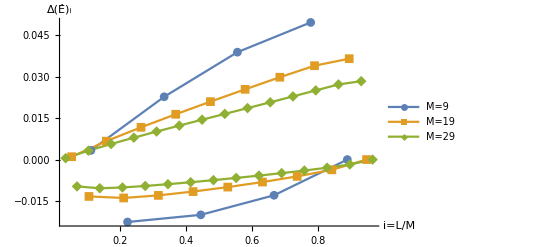
-Graphics-(a) s=1,ξ=0

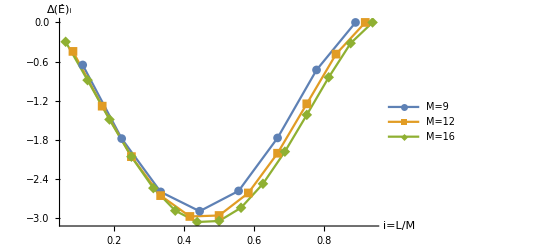
-Graphics-(b) s=2,ξ=0

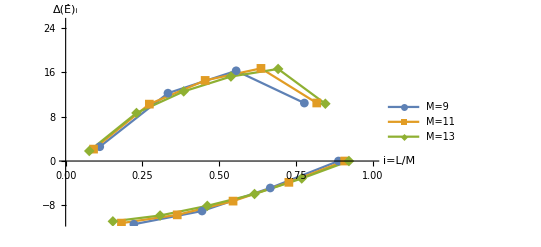
-Graphics-(c) s=3,ξ=0

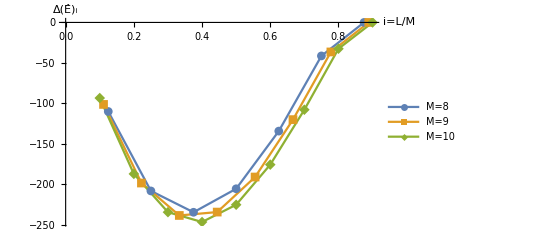
-Graphics-(d) s=4,ξ=0

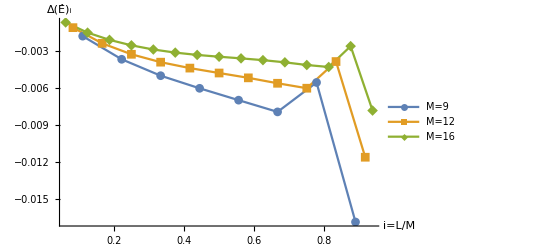
-Graphics-(a) s=2,ξ=1

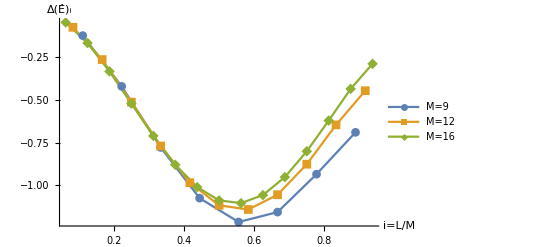
-Graphics-(a) s=2,ξ=2

```mathematica
(* This cell demostrate how Delta Subscript[E, i] changes with respect to i=L/M.*)
p1=PlotEnergyCorrection[1,0,{9,19,29},True, DataSet->1,NormalizeFactorM->2.75,Joined->True,PlotMarkers->Automatic, LegendPos->{0.18,0.75}];
p2=PlotEnergyCorrection[1,0,{9,19,29}, False,DataSet->2,NormalizeFactorM->2.75,Joined->True,PlotMarkers->Automatic];
ps1=Labeled[Show[p1,p2, PlotRange->Automatic],Style["(a) s=1,ξ=0",FontSize->LabelFontSize]]

ps2=Labeled[PlotEnergyCorrection[2,0,{9,12,16}, True,DataSet->0,NormalizeFactorM->3.5,Joined->True,PlotMarkers->Automatic,LegendPos->{0.14,0.17},PlotRange->{{0,1},{0,-3.5}}, AxesOrigin->{0,0}],Style["(b) s=2,ξ=0",FontSize->LabelFontSize]]

p1=PlotEnergyCorrection[3,0,{9,11,13}, True,DataSet->1,NormalizeFactorM->2.25,Joined->True,PlotMarkers->Automatic,LegendPos->{0.16,0.8}];
p2=PlotEnergyCorrection[3,0,{9,11,13}, False,DataSet->2,NormalizeFactorM->2.25,Joined->True,PlotMarkers->Automatic(*,LegendPos->{0.18,0.7}*)];
ps3=Labeled[Show[p1,p2, PlotRange->{{0,1},{-11,25}}],Style["(c) s=3,ξ=0",FontSize->LabelFontSize]]

ps4=Labeled[PlotEnergyCorrection[4,0,{8,9,10}, True,DataSet->0,NormalizeFactorM->3,Joined->True,PlotMarkers->Automatic,LegendPos->{0.87,0.2},(*PlotRange->{{0,1},{0,-3.5}},*) AxesOrigin->{0,0}],Style["(d) s=4,ξ=0",FontSize->LabelFontSize]]

Export["SubEvM-s1xi0.pdf",ps1];
Export["SubEvM-s2xi0.pdf",ps2];
Export["SubEvM-s3xi0.pdf",ps3];
Export["SubEvM-s4xi0.pdf",ps4];

ps2xi1=Labeled[PlotEnergyCorrection[2,1,{9,12,16}, True,DataSet->0,NormalizeFactorM->3.5,Joined->True,PlotMarkers->Automatic,LegendPos->{0.15,0.3},PlotRange->{{0,1},{0,-0.020}}, AxesOrigin->{0,0}],Style["(a) s=2,ξ=1",FontSize->LabelFontSize]]
ps2xi2=Labeled[PlotEnergyCorrection[2,2,{9,12,16}, True,DataSet->0,NormalizeFactorM->3.5,Joined->True,PlotMarkers->Automatic,LegendPos->{0.15,0.3},PlotRange->{{0,1},{0,-2}}, AxesOrigin->{0,0}],Style["(a) s=2,ξ=2",FontSize->LabelFontSize]]

Export["SubEvM-s2xi1.pdf",ps2xi1];
Export["SubEvM-s2xi2.pdf",ps2xi2];

ClearAll[p1,p2,p11,p12,p21,p22,ps1,ps2,ps3,ps4,ps2xi1,ps2xi2];
```

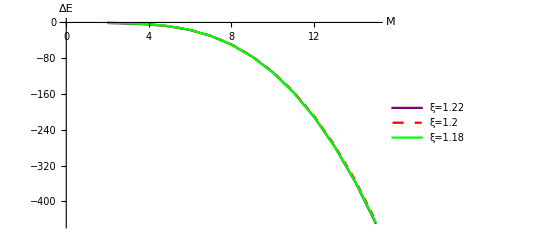

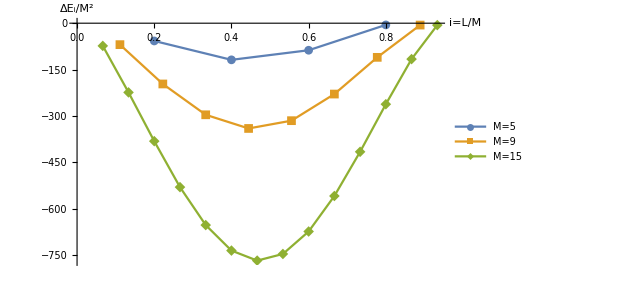

```mathematica
PlotTotalEnergy[{2},{1.22,1.2,1.18},Joined->True,PlotStyle->{Purple,Directive[Red,Dashed],Green},LegendPos->{0.15,0.45}]
PlotEnergyCorrection[2,-.5,{5,9,15}, True,DataSet->0,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic,LegendPos->{0.15,0.2}, AxesOrigin->{0,0}]
```

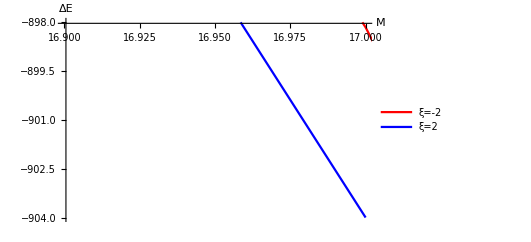

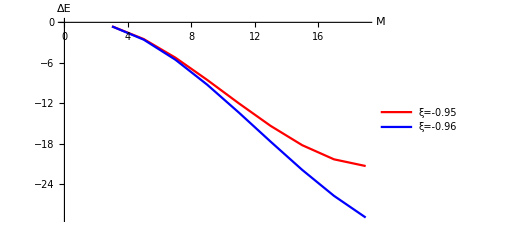

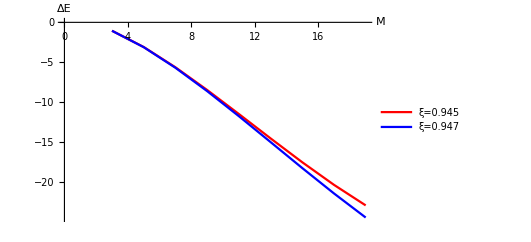

```mathematica
TempFolder = "/users/gaolichen/gitroot/stringbit/build/source/";
PlotTotalEnergy[{1},{-2,2},Joined->True,PlotStyle->{Red,Blue}, LegendPos->{0.18,0.1},Folder->TempFolder,PlotRange->{{16.9,17},{-904,-898}}]
PlotTotalEnergy[{1},{-0.95,-0.96},Joined->True,PlotStyle->{Red,Blue}, LegendPos->{0.18,0.1},Folder->TempFolder]
PlotTotalEnergy[{1},{0.945,0.947},Joined->True,PlotStyle->{Red,Blue}, LegendPos->{0.18,0.1},Folder->TempFolder]
```

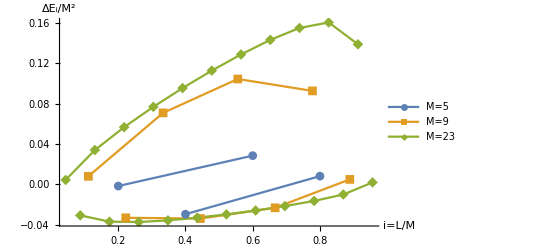

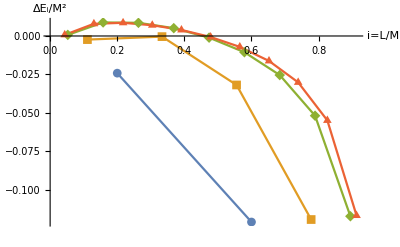

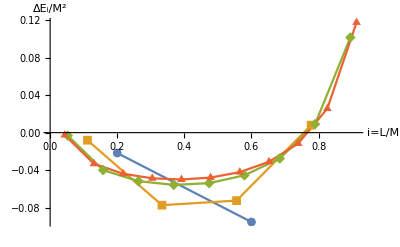

```mathematica
p1=PlotEnergyCorrection[1,0.5,{5,9,23},True, DataSet->1,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic, LegendPos->{0.18,0.7}];
(*Export["SubEvM-s1xi0-a.pdf",%];*)
p2=PlotEnergyCorrection[1,0.5,{5,9,23}, False,DataSet->2,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic];
Show[p1,p2, PlotRange->Automatic]
PlotEnergyCorrection[1,1,{5,9,19,23}, False,DataSet->3,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic]
PlotEnergyCorrection[1,-1,{5,9,19,23}, False,DataSet->3,NormalizeFactorM->2,Joined->True,PlotMarkers->Automatic]
```

```mathematica
ClearAll[PlotGammaV];
PlotGammaV[Mlist_,opts:OptionsPattern[]]:=Module[{data={},i,j},
For[j=1,j≤ Length[Mlist],j++,
AppendTo[data, Table[{i/Mlist[[j]],(GammaV2[Mlist[[j]],i,Numeric->True](*+Cot[(2i+1)Pi/(2Mlist[[j]])]*))/Mlist[[j]]},{i,1,Mlist[[j]]-1}]];
];

ListPlot[data,FilterRules[{opts},Options[ListPlot]]]
];

ClearAll[PlotGammaW];
PlotGammaW[Mlist_,opts:OptionsPattern[]]:=Module[{data={},i,j},
For[j=1,j≤ Length[Mlist],j++,
AppendTo[data, Table[{i/Mlist[[j]],(GammaW2[Mlist[[j]],i,Numeric->True](*+Cot[(2i+1)Pi/(2Mlist[[j]])]*))/Mlist[[j]]},{i,1,Mlist[[j]]-1}]];
];

ListPlot[data,FilterRules[{opts},Options[ListPlot]]]
];
```

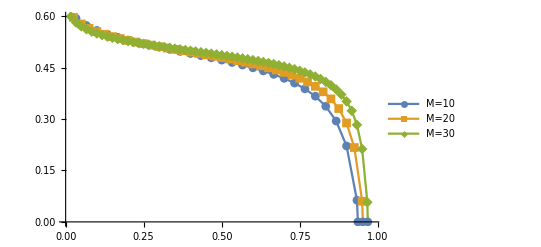

```mathematica
PlotGammaV[{30,40,60},Joined->True, PlotLegends->{"M=10","M=20","M=30","M=40"},PlotMarkers->Automatic]

Clear[tmp1,tmp2,tmp3]
```